```mathematica
SetDirectoryToNotebookLocation[];
```

```mathematica
Needs["DatabaseLink`"];
```

```mathematica
conn=OpenSQLConnection[JDBC["MySQL(Connector/J)","gureckislab.org:3306/active_learn_shj_turk"],"Username"->"lab","Password"->"2research"];
```

```mathematica
res=SQLSelect[conn,"participants",
{"subjid","hitid","assignmentid","beginhit","endhit","status","debriefed","datafile"},(SQLColumn["endhit"]≠Null)&&(SQLColumn["debriefed"]==1)&&SQLColumn["status"]≥3];
```

```mathematica
savedata[sn_,data_]:=Export[StringJoin[{"data/",ToString[sn],".txt"}],data,"String"];
fns=(savedata[#[[1]],#[[-1]]])&/@res
```

{data/1.txt,data/2.txt,data/3.txt,data/4.txt,data/9.txt,data/10.txt,data/11.txt,data/12.txt,data/14.txt,data/16.txt,data/18.txt}

```mathematica
getLearnToCrit[filename_]:=Module[
{data,cond,shjtype,blockstocrit},
data=Import[filename,"CSV"];
cond=data[[1]][[2]];
shjtype=data[[1]][[3]];
blockstocrit=Max[Select[Select[data,Length[#]>6&][[All,6]],NumberQ]]+1;
{{cond,shjtype},blockstocrit}
];
```

```mathematica
btc=Sort[getLearnToCrit/@fns];
active=GatherBy[Select[btc,#[[1,1]]==0&],First];
passive=GatherBy[Select[btc,#[[1,1]]==1&],First];

getMeanBlocks[data_,cond_]:=Module[
{part},
part=Select[data,#[[1,1,2]]==cond&][[All,All,-1]];
If[part≠{},N[Mean[part[[1]]]],0]
];
```

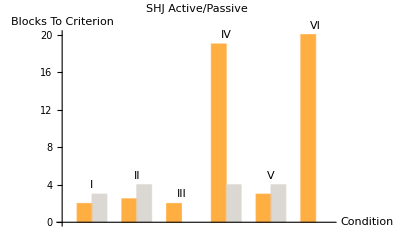
-Graphics--Graphics- | Active
-Graphics- | Passive

```mathematica
BarChart[
Transpose[{getMeanBlocks[active,#-1]&/@Range[6],
getMeanBlocks[passive,#-1]&/@Range[6]}],
PlotRange->{0,20},
ChartLabels->{Placed[{"I","II","III","IV","V","VI"},Above],None},
ChartStyle->{ColorData["Crayola"]["YellowOrange"],
ColorData["Crayola"]["Timberwolf"]},BarSpacing->{0,1},PlotLabel->"SHJ Active/Passive",AxesLabel->{"Condition","Blocks To Criterion"},ChartLegends->{"Active","Passive"}
]
```